```mathematica
two=Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofournull"]]]==2&]
```

{26489,21957,20457,19701,19689,19685,39366,39375,39379,39369,39367,8811,7455,6723,6615,6563,13122,13203,13231,13149,13123,3403,2673,2241,2193,4374,4617,4647,4401,4377,1215,891,747,1458,1701,1791,1539,1467,245,486,487,87,162,165,45,54,63,18,6,2}

```mathematica
three=Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofournull"]]]==4&]
```

{26244,26730,26731,26334,26274,26245,33048,33049,21870,22122,22032,22035,21898,21873,24138,24141,20412,20658,20494,20466,20475,20421,21168,21177,19926,19927,19764,19767,19710,19719,19695,19697,19699,19693,19705,19687,46170,46171,41634,41637,40122,40131,39384,39372,39368,8748,9072,8775,8793,8766,8752,10944,10971,7290,7560,7371,7377,7300,7296,8022,8103,6804,6805,6669,6671,6697,6645,6643,6751,6597,6589,6570,6564,15318,15345,13854,13935,13284,13176,13124,2916,3159,3161,3024,2928,2918,3646,3889,2457,2463,2487,2433,2431,2703,2268,2271,2223,2217,2196,2188,5104,5347,4860,4428,4380,1053,1071,1143,981,973,1305,819,813,756,765,732,730,1944,1620,1476,324,342,328,414,270,280,276,300,252,246,576,516,488,108,120,110,136,90,82,190,168,30,28,72,12,14,16,10,22,4}

```mathematica
large=Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofournull"]]]>30&]
```

{29160,29403,29484,29520,29523,29525,29527,29521,29529,29533,29537,29514,29515,29517,29512,29513,29542,29551,29560,29493,29496,29497,29494,29502,29506,29487,29488,29485,29574,29602,29605,29608,29633,29577,29430,29439,29442,29443,29446,29440,29433,29434,29436,29431,29460,29469,29412,29416,29417,29413,29406,29407,29404,29405,29646,29736,29766,29767,29768,29797,29737,29826,29857,29888,29676,29677,29706,29647,29648,29241,29268,29277,29280,29281,29282,29278,29271,29272,29269,29270,29296,29305,29250,29253,29254,29257,29244,29245,29247,29242,29322,29350,29353,29378,29325,29328,29187,29196,29199,29200,29197,29205,29209,29190,29188,29214,29223,29232,29169,29172,29173,29174,29176,29170,29178,29182,29186,29163,29164,29166,29161,29162,29920,30163,30244,30253,30262,30334,30172,30406,30496,30586,30001,30010,30082,29929,29938,28782,28791,28794,28795,28792,28800,28804,28785,28786,28783,28767,28768,28765,28777,28758,28759,28756,28873,28876,28848,28701,28710,28713,28714,28711,28704,28705,28702,28686,28687,28684,28677,28678,28675,29037,29038,29008,29128,28947,28948,28918,28539,28548,28551,28552,28549,28542,28543,28540,28524,28525,28522,28515,28516,28513,28621,28624,28596,28458,28467,28470,28471,28468,28476,28480,28461,28462,28459,28443,28444,28441,28453,28434,28435,28432,31438,31681,31708,31711,31714,31738,31684,31924,31954,31984,31465,31468,31492,31441,31444,32198,32441,32684,30978,30981,30954,31224,30735,30738,30711,27297,27324,27333,27336,27337,27340,27334,27327,27328,27330,27325,27355,27364,27306,27309,27310,27307,27300,27301,27298,27252,27255,27256,27259,27253,27247,27244,27282,27225,27228,27229,27226,27220,27217,27549,27579,27580,27610,27550,27490,27460,27054,27081,27090,27093,27094,27091,27084,27085,27082,27109,27118,27063,27066,27067,27070,27064,27057,27058,27060,27055,27009,27012,27013,27010,27004,27001,27036,26982,26985,26986,26989,26983,26977,26974,28056,28065,27984,28308,27813,27822,27741,26595,26604,26608,26609,26605,26598,26599,26596,26597,26580,26581,26578,26571,26572,26569,26523,26526,26527,26524,26518,26515,26499,26500,26501,26497,26491,26850,26851,26852,26821,26761,26352,26361,26364,26365,26366,26362,26355,26356,26353,26354,26337,26338,26335,26328,26326,26280,26283,26284,26275,26272,26256,26257,26258,26254,26248,35976,36057,36084,36085,36086,36112,36058,36138,36166,36194,36003,36004,36030,35977,35978,36736,36817,36898,35352,35353,35326,35434,35271,35272,35245,38254,38281,38308,39014,37548,33861,33888,33889,33916,33862,33808,33781,34620,33156,33157,33158,33130,33076,22842,22923,22950,22959,22962,22963,22964,22960,22953,22954,22951,22952,22981,22990,22932,22935,22936,22933,22926,22927,22924,23013,23041,23044,23072,23016,22869,22878,22881,22882,22879,22872,22873,22870,22899,22908,22851,22854,22855,22856,22852,22845,22846,22843,22844,22716,22719,22720,22721,22717,22710,22711,22744,22689,22692,22693,22690,22683,22684,22792,22764,22635,22638,22639,22636,22629,22630,22662,22608,22611,22612,22613,22609,22602,22603,23599,23680,23689,23770,23608,23446,23365,22221,22230,22233,22234,22237,22224,22225,22227,22222,22206,22207,22204,22197,22198,22195,22312,22315,22318,22287,22140,22149,22152,22153,22156,22150,22143,22144,22146,22141,22125,22126,22123,22116,22114,21987,21990,21991,21988,21981,21982,21963,21964,21967,21961,21955,22063,21906,21910,21907,21900,21901,21882,21883,21886,21880,21874,25111,25138,25141,25168,25114,24898,24871,25868,24408,24411,24414,24384,24168,20736,20763,20772,20775,20776,20773,20781,20785,20766,20764,20794,20803,20812,20745,20748,20749,20746,20754,20758,20739,20740,20737,20691,20694,20695,20692,20686,20683,20721,20664,20667,20668,20659,20656,20529,20532,20533,20530,20523,20524,20557,20502,20506,20503,20496,20497,20451,20452,20449,20461,20443,20424,20425,20422,20434,20416,21492,21501,21510,21420,21258,20034,20043,20046,20047,20048,20050,20044,20052,20056,20060,20037,20038,20040,20035,20036,20019,20020,20017,20029,20010,20011,20008,19962,19965,19966,19969,19963,19957,19954,19938,19939,19940,19936,19930,19800,19803,19804,19805,19801,19794,19795,19776,19777,19780,19774,19768,19722,19723,19720,19732,19714,49194,49203,49206,49207,49208,49210,49204,49212,49216,49220,49197,49198,49200,49195,49196,49954,49963,49972,48450,48451,48448,48460,48441,48442,48439,51472,51475,51478,52232,50718,46935,46938,46939,46942,46936,46930,46927,47694,46182,46183,46184,46180,46174,56010,56011,56012,56770,55252,58288,59048,53734,42399,42402,42403,42404,42400,42393,42394,43156,41646,41647,41650,41644,41638,44662,40134,40135,40132,40144,40126,9720,9801,9828,9837,9840,9841,9842,9844,9838,9846,9850,9854,9831,9832,9834,9829,9830,9810,9813,9814,9811,9819,9823,9804,9805,9802,9747,9756,9759,9760,9763,9757,9750,9751,9753,9748,9729,9732,9733,9734,9730,9723,9724,9721,9722,9558,9585,9594,9597,9598,9599,9595,9588,9589,9586,9587,9567,9570,9571,9574,9568,9561,9562,9564,9559,9504,9513,9516,9517,9514,9522,9526,9507,9508,9505,10453,10534,10543,10552,10462,10291,10300,9099,9108,9111,9112,9109,9117,9121,9102,9103,9100,9130,9139,9148,9084,9082,9094,9075,9076,9073,9018,9027,9030,9031,9028,9021,9022,9048,9057,9003,9004,9001,8994,8995,8992,8856,8865,8868,8869,8866,8860,8857,8884,8893,8841,8842,8839,8832,8833,8830,8787,8788,8785,8797,8778,8779,8776,11917,11944,11947,11950,11920,11701,11704,12650,11214,11217,11244,11190,10974,7614,7641,7650,7653,7654,7657,7651,7644,7645,7647,7642,7623,7626,7627,7624,7617,7618,7704,7732,7735,7738,7707,7569,7572,7576,7570,7564,7561,7542,7545,7546,7543,7537,7534,7398,7410,7411,7408,7401,7402,7399,7380,7383,7384,7387,7381,7375,7372,7480,7483,7326,7329,7330,7327,7321,7318,8346,8355,8436,8274,8112,6912,6921,6924,6925,6926,6922,6915,6916,6913,6914,6943,6952,6897,6898,6895,6888,6889,6886,7003,7006,7034,6978,6840,6843,6844,6841,6835,6832,6870,6816,6817,6818,6814,6808,6678,6681,6682,6683,6679,6672,6673,6706,6654,6655,6652,6646,6754,6600,6601,6598,6592,16131,16158,16159,16160,16132,16077,16078,16864,15426,15427,15454,15400,15346,18274,13962,13963,13936,14044,13882,3240,3267,3276,3279,3280,3281,3277,3270,3271,3268,3269,3249,3252,3253,3250,3244,3241,3186,3198,3199,3196,3189,3190,3187,3168,3171,3172,3173,3169,3162,3163,3492,3522,3523,3524,3493,3432,3433,3033,3036,3038,3034,3027,3028,3006,3009,3010,3007,3000,3001,2952,2955,2956,2953,2946,2947,3970,3979,3898,4222,3736,2538,2547,2550,2551,2554,2548,2541,2542,2544,2539,2569,2578,2523,2524,2521,2514,2515,2512,2466,2469,2470,2473,2467,2461,2458,2496,2442,2443,2440,2434,2793,2794,2824,2764,2704,2304,2307,2308,2305,2298,2299,2332,2280,2281,2284,2278,2272,2226,2227,2224,2218,5374,5377,5350,5620,5134,1080,1089,1092,1093,1090,1098,1102,1083,1084,1081,1065,1066,1063,1075,1056,1057,1054,1171,1174,1146,1008,1011,1012,1009,1003,1000,984,985,982,976,1335,1336,1306,1426,1246,846,849,850,847,840,841,822,823,820,814,922,768,769,766,778,760}

```mathematica
Table[Simplify[allGraphs[k,"comp"][allGraphs[k,"colofournull"],0]],{k,three}]/.repBaseNullGraph
```

{-Graphics-19683p12x3x4x5+-Graphics-6561p13x2x4x5+-Graphics-26487p123x4x5>-Graphics-243p1x23x4x5,-Graphics-19683p12x3x4x5+-Graphics-6561p13x2x4x5>-Graphics-243p1x23x4x5+-Graphics-26487p123x4x5,-Graphics-19684p12x3x45+-Graphics-6562p13x2x45>-Graphics-244p1x23x45+-Graphics-26488p123x45,-Graphics-19692p12x34x5+-Graphics-6642p13x24x5+-Graphics-28764p1234x5>-Graphics-2430p14x23x5,-Graphics-19686p12x35x4+-Graphics-6588p13x25x4+-Graphics-27246p1235x4>-Graphics-972p15x23x4,-Graphics-19684p12x3x45+-Graphics-6562p13x2x45+-Graphics-26488p123x45>-Graphics-244p1x23x45,-Graphics-19683p12x3x4x5+-Graphics-243p1x23x4x5>-Graphics-6561p13x2x4x5+-Graphics-26487p123x4x5,-Graphics-19684p12x3x45+-Graphics-244p1x23x45>-Graphics-6562p13x2x45+-Graphics-26488p123x45,-Graphics-19683p12x3x4x5+-Graphics-2187p14x2x3x5+-Graphics-21951p124x3x5>-Graphics-81p1x24x3x5,-Graphics-19692p12x34x5+-Graphics-2430p14x23x5+-Graphics-28764p1234x5>-Graphics-6642p13x24x5,-Graphics-19683p12x3x4x5+-Graphics-2187p14x2x3x5>-Graphics-81p1x24x3x5+-Graphics-21951p124x3x5,-Graphics-19686p12x35x4+-Graphics-2190p14x2x35>-Graphics-84p1x24x35+-Graphics-21954p124x35,-Graphics-19684p12x3x45+-Graphics-2214p14x25x3+-Graphics-22708p1245x3>-Graphics-810p15x24x3,-Graphics-19686p12x35x4+-Graphics-2190p14x2x35+-Graphics-21954p124x35>-Graphics-84p1x24x35,-Graphics-19683p12x3x4x5+-Graphics-81p1x24x3x5>-Graphics-2187p14x2x3x5+-Graphics-21951p124x3x5,-Graphics-19686p12x35x4+-Graphics-84p1x24x35>-Graphics-2190p14x2x35+-Graphics-21954p124x35,-Graphics-19683p12x3x4x5+-Graphics-729p15x2x3x4+-Graphics-20439p125x3x4>-Graphics-27p1x25x3x4,-Graphics-19686p12x35x4+-Graphics-972p15x23x4+-Graphics-27246p1235x4>-Graphics-6588p13x25x4,-Graphics-19684p12x3x45+-Graphics-810p15x24x3+-Graphics-22708p1245x3>-Graphics-2214p14x25x3,-Graphics-19683p12x3x4x5+-Graphics-729p15x2x3x4>-Graphics-27p1x25x3x4+-Graphics-20439p125x3x4,-Graphics-19692p12x34x5+-Graphics-738p15x2x34>-Graphics-36p1x25x34+-Graphics-20448p125x34,-Graphics-19692p12x34x5+-Graphics-738p15x2x34+-Graphics-20448p125x34>-Graphics-36p1x25x34,-Graphics-19683p12x3x4x5+-Graphics-27p1x25x3x4>-Graphics-729p15x2x3x4+-Graphics-20439p125x3x4,-Graphics-19692p12x34x5+-Graphics-36p1x25x34>-Graphics-738p15x2x34+-Graphics-20448p125x34,-Graphics-19683p12x3x4x5+-Graphics-243p1x23x4x5+-Graphics-26487p123x4x5>-Graphics-6561p13x2x4x5,-Graphics-19684p12x3x45+-Graphics-244p1x23x45+-Graphics-26488p123x45>-Graphics-6562p13x2x45,-Graphics-19683p12x3x4x5+-Graphics-81p1x24x3x5+-Graphics-21951p124x3x5>-Graphics-2187p14x2x3x5,-Graphics-19686p12x35x4+-Graphics-84p1x24x35+-Graphics-21954p124x35>-Graphics-2190p14x2x35,-Graphics-19683p12x3x4x5+-Graphics-27p1x25x3x4+-Graphics-20439p125x3x4>-Graphics-729p15x2x3x4,-Graphics-19692p12x34x5+-Graphics-36p1x25x34+-Graphics-20448p125x34>-Graphics-738p15x2x34,-Graphics-19692p12x34x5+-Graphics-19686p12x35x4+-Graphics-19696p12x345>-Graphics-19684p12x3x45,-Graphics-19692p12x34x5+-Graphics-19686p12x35x4>-Graphics-19684p12x3x45+-Graphics-19696p12x345,-Graphics-19692p12x34x5+-Graphics-19684p12x3x45>-Graphics-19686p12x35x4+-Graphics-19696p12x345,-Graphics-19692p12x34x5+-Graphics-19684p12x3x45+-Graphics-19696p12x345>-Graphics-19686p12x35x4,-Graphics-19686p12x35x4+-Graphics-19684p12x3x45>-Graphics-19692p12x34x5+-Graphics-19696p12x345,-Graphics-19686p12x35x4+-Graphics-19684p12x3x45+-Graphics-19696p12x345>-Graphics-19692p12x34x5,-Graphics-6561p13x2x4x5+-Graphics-243p1x23x4x5>-Graphics-19683p12x3x4x5+-Graphics-26487p123x4x5,-Graphics-6562p13x2x45+-Graphics-244p1x23x45>-Graphics-19684p12x3x45+-Graphics-26488p123x45,-Graphics-2187p14x2x3x5+-Graphics-81p1x24x3x5>-Graphics-19683p12x3x4x5+-Graphics-21951p124x3x5,-Graphics-2190p14x2x35+-Graphics-84p1x24x35>-Graphics-19686p12x35x4+-Graphics-21954p124x35,-Graphics-729p15x2x3x4+-Graphics-27p1x25x3x4>-Graphics-19683p12x3x4x5+-Graphics-20439p125x3x4,-Graphics-738p15x2x34+-Graphics-36p1x25x34>-Graphics-19692p12x34x5+-Graphics-20448p125x34,-Graphics-0p1x2x3x4x5+-Graphics-19692p12x34x5>-Graphics-19683p12x3x4x5+-Graphics-9p1x2x34x5,-Graphics-0p1x2x3x4x5+-Graphics-19686p12x35x4>-Graphics-19683p12x3x4x5+-Graphics-3p1x2x35x4,-Graphics-0p1x2x3x4x5+-Graphics-19684p12x3x45>-Graphics-19683p12x3x4x5+-Graphics-1p1x2x3x45,-Graphics-6561p13x2x4x5+-Graphics-2187p14x2x3x5+-Graphics-8757p134x2x5>-Graphics-9p1x2x34x5,-Graphics-6642p13x24x5+-Graphics-2430p14x23x5+-Graphics-28764p1234x5>-Graphics-19692p12x34x5,-Graphics-6588p13x25x4+-Graphics-2214p14x25x3+-Graphics-8784p134x25>-Graphics-36p1x25x34,-Graphics-6588p13x25x4+-Graphics-2214p14x25x3>-Graphics-36p1x25x34+-Graphics-8784p134x25,-Graphics-6561p13x2x4x5+-Graphics-2187p14x2x3x5>-Graphics-9p1x2x34x5+-Graphics-8757p134x2x5,-Graphics-6562p13x2x45+-Graphics-2190p14x2x35+-Graphics-9490p1345x2>-Graphics-738p15x2x34,-Graphics-6561p13x2x4x5+-Graphics-9p1x2x34x5>-Graphics-2187p14x2x3x5+-Graphics-8757p134x2x5,-Graphics-6588p13x25x4+-Graphics-36p1x25x34>-Graphics-2214p14x25x3+-Graphics-8784p134x25,-Graphics-6561p13x2x4x5+-Graphics-729p15x2x3x4+-Graphics-7293p135x2x4>-Graphics-3p1x2x35x4,-Graphics-6588p13x25x4+-Graphics-972p15x23x4+-Graphics-27246p1235x4>-Graphics-19686p12x35x4,-Graphics-6642p13x24x5+-Graphics-810p15x24x3+-Graphics-7374p135x24>-Graphics-84p1x24x35,-Graphics-6642p13x24x5+-Graphics-810p15x24x3>-Graphics-84p1x24x35+-Graphics-7374p135x24,-Graphics-6562p13x2x45+-Graphics-738p15x2x34+-Graphics-9490p1345x2>-Graphics-2190p14x2x35,-Graphics-6561p13x2x4x5+-Graphics-729p15x2x3x4>-Graphics-3p1x2x35x4+-Graphics-7293p135x2x4,-Graphics-6561p13x2x4x5+-Graphics-3p1x2x35x4>-Graphics-729p15x2x3x4+-Graphics-7293p135x2x4,-Graphics-6642p13x24x5+-Graphics-84p1x24x35>-Graphics-810p15x24x3+-Graphics-7374p135x24,-Graphics-6561p13x2x4x5+-Graphics-243p1x23x4x5+-Graphics-26487p123x4x5>-Graphics-19683p12x3x4x5,-Graphics-6562p13x2x45+-Graphics-244p1x23x45+-Graphics-26488p123x45>-Graphics-19684p12x3x45,-Graphics-6642p13x24x5+-Graphics-6588p13x25x4+-Graphics-6670p13x245>-Graphics-6562p13x2x45,-Graphics-6642p13x24x5+-Graphics-6588p13x25x4>-Graphics-6562p13x2x45+-Graphics-6670p13x245,-Graphics-6642p13x24x5+-Graphics-6562p13x2x45>-Graphics-6588p13x25x4+-Graphics-6670p13x245,-Graphics-6642p13x24x5+-Graphics-84p1x24x35+-Graphics-7374p135x24>-Graphics-810p15x24x3,-Graphics-6642p13x24x5+-Graphics-6562p13x2x45+-Graphics-6670p13x245>-Graphics-6588p13x25x4,-Graphics-6588p13x25x4+-Graphics-6562p13x2x45>-Graphics-6642p13x24x5+-Graphics-6670p13x245,-Graphics-6588p13x25x4+-Graphics-36p1x25x34+-Graphics-8784p134x25>-Graphics-2214p14x25x3,-Graphics-6588p13x25x4+-Graphics-6562p13x2x45+-Graphics-6670p13x245>-Graphics-6642p13x24x5,-Graphics-6561p13x2x4x5+-Graphics-9p1x2x34x5+-Graphics-8757p134x2x5>-Graphics-2187p14x2x3x5,-Graphics-6561p13x2x4x5+-Graphics-3p1x2x35x4+-Graphics-7293p135x2x4>-Graphics-729p15x2x3x4,-Graphics-2187p14x2x3x5+-Graphics-9p1x2x34x5>-Graphics-6561p13x2x4x5+-Graphics-8757p134x2x5,-Graphics-2214p14x25x3+-Graphics-36p1x25x34>-Graphics-6588p13x25x4+-Graphics-8784p134x25,-Graphics-729p15x2x3x4+-Graphics-3p1x2x35x4>-Graphics-6561p13x2x4x5+-Graphics-7293p135x2x4,-Graphics-810p15x24x3+-Graphics-84p1x24x35>-Graphics-6642p13x24x5+-Graphics-7374p135x24,-Graphics-0p1x2x3x4x5+-Graphics-6642p13x24x5>-Graphics-6561p13x2x4x5+-Graphics-81p1x24x3x5,-Graphics-0p1x2x3x4x5+-Graphics-6588p13x25x4>-Graphics-6561p13x2x4x5+-Graphics-27p1x25x3x4,-Graphics-0p1x2x3x4x5+-Graphics-6562p13x2x45>-Graphics-6561p13x2x4x5+-Graphics-1p1x2x3x45,-Graphics-2187p14x2x3x5+-Graphics-729p15x2x3x4+-Graphics-2917p145x2x3>-Graphics-1p1x2x3x45,-Graphics-2430p14x23x5+-Graphics-972p15x23x4+-Graphics-3160p145x23>-Graphics-244p1x23x45,-Graphics-2430p14x23x5+-Graphics-972p15x23x4>-Graphics-244p1x23x45+-Graphics-3160p145x23,-Graphics-2214p14x25x3+-Graphics-810p15x24x3+-Graphics-22708p1245x3>-Graphics-19684p12x3x45,-Graphics-2190p14x2x35+-Graphics-738p15x2x34+-Graphics-9490p1345x2>-Graphics-6562p13x2x45,-Graphics-2187p14x2x3x5+-Graphics-729p15x2x3x4>-Graphics-1p1x2x3x45+-Graphics-2917p145x2x3,-Graphics-2187p14x2x3x5+-Graphics-1p1x2x3x45>-Graphics-729p15x2x3x4+-Graphics-2917p145x2x3,-Graphics-2430p14x23x5+-Graphics-244p1x23x45>-Graphics-972p15x23x4+-Graphics-3160p145x23,-Graphics-2430p14x23x5+-Graphics-2214p14x25x3+-Graphics-2460p14x235>-Graphics-2190p14x2x35,-Graphics-2430p14x23x5+-Graphics-2214p14x25x3>-Graphics-2190p14x2x35+-Graphics-2460p14x235,-Graphics-2430p14x23x5+-Graphics-2190p14x2x35>-Graphics-2214p14x25x3+-Graphics-2460p14x235,-Graphics-2430p14x23x5+-Graphics-2190p14x2x35+-Graphics-2460p14x235>-Graphics-2214p14x25x3,-Graphics-2430p14x23x5+-Graphics-244p1x23x45+-Graphics-3160p145x23>-Graphics-972p15x23x4,-Graphics-2214p14x25x3+-Graphics-2190p14x2x35>-Graphics-2430p14x23x5+-Graphics-2460p14x235,-Graphics-2187p14x2x3x5+-Graphics-81p1x24x3x5+-Graphics-21951p124x3x5>-Graphics-19683p12x3x4x5,-Graphics-2190p14x2x35+-Graphics-84p1x24x35+-Graphics-21954p124x35>-Graphics-19686p12x35x4,-Graphics-2214p14x25x3+-Graphics-36p1x25x34+-Graphics-8784p134x25>-Graphics-6588p13x25x4,-Graphics-2214p14x25x3+-Graphics-2190p14x2x35+-Graphics-2460p14x235>-Graphics-2430p14x23x5,-Graphics-2187p14x2x3x5+-Graphics-9p1x2x34x5+-Graphics-8757p134x2x5>-Graphics-6561p13x2x4x5,-Graphics-2187p14x2x3x5+-Graphics-1p1x2x3x45+-Graphics-2917p145x2x3>-Graphics-729p15x2x3x4,-Graphics-729p15x2x3x4+-Graphics-1p1x2x3x45>-Graphics-2187p14x2x3x5+-Graphics-2917p145x2x3,-Graphics-972p15x23x4+-Graphics-244p1x23x45>-Graphics-2430p14x23x5+-Graphics-3160p145x23,-Graphics-0p1x2x3x4x5+-Graphics-2430p14x23x5>-Graphics-2187p14x2x3x5+-Graphics-243p1x23x4x5,-Graphics-0p1x2x3x4x5+-Graphics-2214p14x25x3>-Graphics-2187p14x2x3x5+-Graphics-27p1x25x3x4,-Graphics-0p1x2x3x4x5+-Graphics-2190p14x2x35>-Graphics-2187p14x2x3x5+-Graphics-3p1x2x35x4,-Graphics-972p15x23x4+-Graphics-810p15x24x3+-Graphics-1062p15x234>-Graphics-738p15x2x34,-Graphics-972p15x23x4+-Graphics-810p15x24x3>-Graphics-738p15x2x34+-Graphics-1062p15x234,-Graphics-972p15x23x4+-Graphics-738p15x2x34>-Graphics-810p15x24x3+-Graphics-1062p15x234,-Graphics-972p15x23x4+-Graphics-738p15x2x34+-Graphics-1062p15x234>-Graphics-810p15x24x3,-Graphics-972p15x23x4+-Graphics-244p1x23x45+-Graphics-3160p145x23>-Graphics-2430p14x23x5,-Graphics-810p15x24x3+-Graphics-738p15x2x34>-Graphics-972p15x23x4+-Graphics-1062p15x234,-Graphics-810p15x24x3+-Graphics-738p15x2x34+-Graphics-1062p15x234>-Graphics-972p15x23x4,-Graphics-810p15x24x3+-Graphics-84p1x24x35+-Graphics-7374p135x24>-Graphics-6642p13x24x5,-Graphics-729p15x2x3x4+-Graphics-27p1x25x3x4+-Graphics-20439p125x3x4>-Graphics-19683p12x3x4x5,-Graphics-738p15x2x34+-Graphics-36p1x25x34+-Graphics-20448p125x34>-Graphics-19692p12x34x5,-Graphics-729p15x2x3x4+-Graphics-3p1x2x35x4+-Graphics-7293p135x2x4>-Graphics-6561p13x2x4x5,-Graphics-729p15x2x3x4+-Graphics-1p1x2x3x45+-Graphics-2917p145x2x3>-Graphics-2187p14x2x3x5,-Graphics-0p1x2x3x4x5+-Graphics-972p15x23x4>-Graphics-729p15x2x3x4+-Graphics-243p1x23x4x5,-Graphics-0p1x2x3x4x5+-Graphics-810p15x24x3>-Graphics-729p15x2x3x4+-Graphics-81p1x24x3x5,-Graphics-0p1x2x3x4x5+-Graphics-738p15x2x34>-Graphics-729p15x2x3x4+-Graphics-9p1x2x34x5,-Graphics-243p1x23x4x5+-Graphics-81p1x24x3x5+-Graphics-333p1x234x5>-Graphics-9p1x2x34x5,-Graphics-243p1x23x4x5+-Graphics-81p1x24x3x5>-Graphics-9p1x2x34x5+-Graphics-333p1x234x5,-Graphics-244p1x23x45+-Graphics-84p1x24x35+-Graphics-364p1x2345>-Graphics-36p1x25x34,-Graphics-243p1x23x4x5+-Graphics-9p1x2x34x5>-Graphics-81p1x24x3x5+-Graphics-333p1x234x5,-Graphics-243p1x23x4x5+-Graphics-27p1x25x3x4+-Graphics-273p1x235x4>-Graphics-3p1x2x35x4,-Graphics-244p1x23x45+-Graphics-36p1x25x34+-Graphics-364p1x2345>-Graphics-84p1x24x35,-Graphics-243p1x23x4x5+-Graphics-27p1x25x3x4>-Graphics-3p1x2x35x4+-Graphics-273p1x235x4,-Graphics-243p1x23x4x5+-Graphics-3p1x2x35x4>-Graphics-27p1x25x3x4+-Graphics-273p1x235x4,-Graphics-243p1x23x4x5+-Graphics-9p1x2x34x5+-Graphics-333p1x234x5>-Graphics-81p1x24x3x5,-Graphics-243p1x23x4x5+-Graphics-3p1x2x35x4+-Graphics-273p1x235x4>-Graphics-27p1x25x3x4,-Graphics-81p1x24x3x5+-Graphics-9p1x2x34x5>-Graphics-243p1x23x4x5+-Graphics-333p1x234x5,-Graphics-27p1x25x3x4+-Graphics-3p1x2x35x4>-Graphics-243p1x23x4x5+-Graphics-273p1x235x4,-Graphics-0p1x2x3x4x5+-Graphics-244p1x23x45>-Graphics-243p1x23x4x5+-Graphics-1p1x2x3x45,-Graphics-81p1x24x3x5+-Graphics-27p1x25x3x4+-Graphics-109p1x245x3>-Graphics-1p1x2x3x45,-Graphics-84p1x24x35+-Graphics-36p1x25x34+-Graphics-364p1x2345>-Graphics-244p1x23x45,-Graphics-81p1x24x3x5+-Graphics-27p1x25x3x4>-Graphics-1p1x2x3x45+-Graphics-109p1x245x3,-Graphics-81p1x24x3x5+-Graphics-1p1x2x3x45>-Graphics-27p1x25x3x4+-Graphics-109p1x245x3,-Graphics-81p1x24x3x5+-Graphics-9p1x2x34x5+-Graphics-333p1x234x5>-Graphics-243p1x23x4x5,-Graphics-81p1x24x3x5+-Graphics-1p1x2x3x45+-Graphics-109p1x245x3>-Graphics-27p1x25x3x4,-Graphics-27p1x25x3x4+-Graphics-1p1x2x3x45>-Graphics-81p1x24x3x5+-Graphics-109p1x245x3,-Graphics-0p1x2x3x4x5+-Graphics-84p1x24x35>-Graphics-81p1x24x3x5+-Graphics-3p1x2x35x4,-Graphics-27p1x25x3x4+-Graphics-3p1x2x35x4+-Graphics-273p1x235x4>-Graphics-243p1x23x4x5,-Graphics-27p1x25x3x4+-Graphics-1p1x2x3x45+-Graphics-109p1x245x3>-Graphics-81p1x24x3x5,-Graphics-0p1x2x3x4x5+-Graphics-36p1x25x34>-Graphics-27p1x25x3x4+-Graphics-9p1x2x34x5,-Graphics-9p1x2x34x5+-Graphics-3p1x2x35x4+-Graphics-13p1x2x345>-Graphics-1p1x2x3x45,-Graphics-9p1x2x34x5+-Graphics-3p1x2x35x4>-Graphics-1p1x2x3x45+-Graphics-13p1x2x345,-Graphics-9p1x2x34x5+-Graphics-1p1x2x3x45>-Graphics-3p1x2x35x4+-Graphics-13p1x2x345,-Graphics-9p1x2x34x5+-Graphics-1p1x2x3x45+-Graphics-13p1x2x345>-Graphics-3p1x2x35x4,-Graphics-3p1x2x35x4+-Graphics-1p1x2x3x45>-Graphics-9p1x2x34x5+-Graphics-13p1x2x345,-Graphics-3p1x2x35x4+-Graphics-1p1x2x3x45+-Graphics-13p1x2x345>-Graphics-9p1x2x34x5}

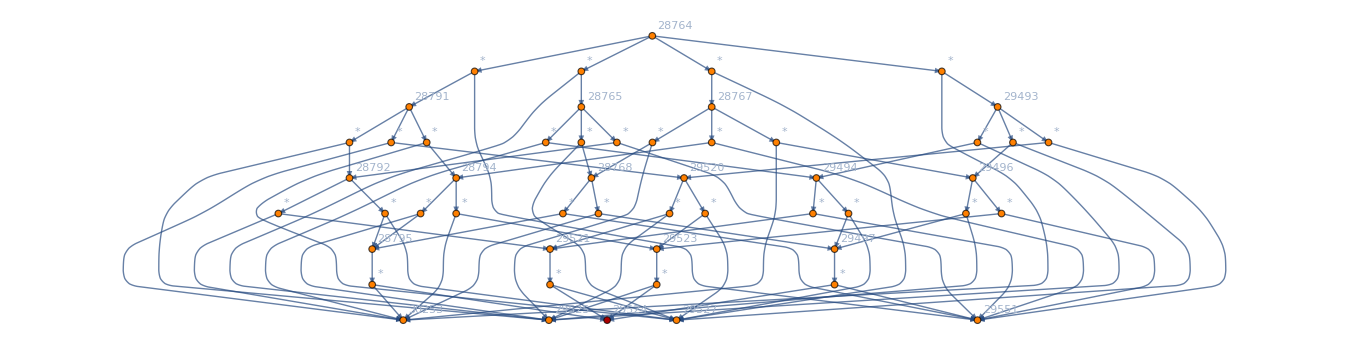

```mathematica
Graph[DependencyGraph[allGraphs,28764],GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
Graph[ExpressionsToGraph[Join[Select[PositiveExpressions,Length[#]>2&],{allGraphs[lambdaKey,"colofour"]}]],GraphLayout->"HighDimensionalEmbedding", GraphHighlight->important, GraphHighlightStyle->"VertexConcaveDiamond",ImageSize->600]
```

```mathematica
repZero2=Table[allGraphs[k,"colofour"]->0,{k,Select[Keys[allGraphs],allGraphs[#,"comp"]==Equal&]}]
```

{v1x2x3x4x5→0,v1x24x35→0,v14x2x35→0,v14x25x3→0,v13x25x4→0,v13x24x5→0}

```mathematica
GraphDu
```